# Решение японского кроссворда методом перебора

## Введение. Основные идеи

Японский кроссворд — это известная головоломка, ответом которой является рисунок. Что это такое и как это решать, можно почитать на Википедии.

Идея решения методом перебора заключается в том, чтобы создать списки всевозможных расположений клеток для всех строк и столбцов. После этого найти те клетки, информация о которых будет точно известна. Затем отсеять такие расположения, которые противоречат найденной информации. Интуитивно понятно, что если циклически повторять последние две процедуры, то можно найти информацию о любой клетке.

## Составление всевозможных расположений

Рассмотрим конкретный пример. Необходимо найти всевозможные расположения для таких данных:

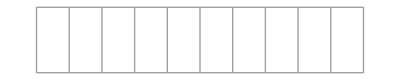
1 | 2 | 3 | -Graphics-

1 | 2 | 3 | -Graphics-

Естественно хранить расположение клеток, как список этих клеток. При этом примем такие соглашения:

1 — закрашенная клетка;

0 — незакрашенная клетка;

* — клетка, о которой ничего не известно.

Например, сверху изображен список, который соответствует данному расположению клеток:

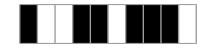
{1,0,0,1,1,0,1,1,1,0}
-Graphics-

Перебор можно осуществить таким образом: поставить в соответствие исходным данным определенные группы клеток и располагать эти группы клеток по порядку в определенном списке (попробуйте самостоятельно подсчитать, сколько элементов должно быть в этом списке). Например:

{1,0} | {1,1,0} | {1,1,1}
 | {0,0,0,0,0} |

Сверху находятся группы (подумайте, почему в последней группе в конце нет нуля), а снизу — список мест (нули), куда их расставлять. Если поставить группы по порядку на места списка с номерами 1, 3 и 4, то получим расположение из примера выше. Таким образом, исходная задача эквивалентна задаче о переборе всех сочетаний из количества мест по количеству групп. Итак, для данной задачи будет 10 всевозможных расположений. Если вы ничего не поняли, тогда просто читайте дальше, возможно, что глядя на код вы все поймете.

Для того, чтобы перебрать всевозможные номера мест, возпользуемся встроенной функцией Subsets. Для нашей задачи эта функция имеет вид:

```mathematica
Subsets[{1,2,3,4,5}, {3}]
```

{{1,2,3},{1,2,4},{1,2,5},{1,3,4},{1,3,5},{1,4,5},{2,3,4},{2,3,5},{2,4,5},{3,4,5}}

Итак, мы получили список всех возможных мест, куда мы можем поставить наши группы. Идея понятна, поэтому напишем программу, которая принимает число — длину поля (количества клеток в сетке, где нужно зарисовывать клетки; в примере — 10) и список — ключ (цифры, что стоят слева от сетки; в примере — 1, 2, 3).

```mathematica
len = 10
clue = {1, 2, 3}
```

10

{1,2,3}

Напишем теперь функцию, которая построит на основе ключа группы клеток для расстановки. В этом нам помогут функции ConstantArray, Append и Delete.

```mathematica
groups = Delete[Append[ConstantArray[1, #], 0]& /@ clue, {-1, -1}]
```

{{1,0},{1,1,0},{1,1,1}}

А также функцию, создающую список мест:

```mathematica
positions = ConstantArray[0, len - Total[clue] + 1]
```

{0,0,0,0,0}

Самое важное сейчас — создаем список всевозможных мест, куда будем ставить группы.

```mathematica
sub = Subsets[Range[len - Total[clue] + 1], {Length[clue]}]
```

{{1,2,3},{1,2,4},{1,2,5},{1,3,4},{1,3,5},{1,4,5},{2,3,4},{2,3,5},{2,4,5},{3,4,5}}

Прежде, чем подставлять группы на места, необходимо составить список замен. Для этого есть очень полезная функция MapThread.

```mathematica
rep = MapThread[Function[{x, y}, x->y], {#, groups}]& /@ sub
```

{{1→{1,0},2→{1,1,0},3→{1,1,1}},{1→{1,0},2→{1,1,0},4→{1,1,1}},{1→{1,0},2→{1,1,0},5→{1,1,1}},{1→{1,0},3→{1,1,0},4→{1,1,1}},{1→{1,0},3→{1,1,0},5→{1,1,1}},{1→{1,0},4→{1,1,0},5→{1,1,1}},{2→{1,0},3→{1,1,0},4→{1,1,1}},{2→{1,0},3→{1,1,0},5→{1,1,1}},{2→{1,0},4→{1,1,0},5→{1,1,1}},{3→{1,0},4→{1,1,0},5→{1,1,1}}}

Финальная стадия — расстановка на свои места. Тут, конечно, необходимо не забыть Flatten.

```mathematica
all = Flatten[ReplacePart[positions, #]]& /@ rep
```

{{1,0,1,1,0,1,1,1,0,0},{1,0,1,1,0,0,1,1,1,0},{1,0,1,1,0,0,0,1,1,1},{1,0,0,1,1,0,1,1,1,0},{1,0,0,1,1,0,0,1,1,1},{1,0,0,0,1,1,0,1,1,1},{0,1,0,1,1,0,1,1,1,0},{0,1,0,1,1,0,0,1,1,1},{0,1,0,0,1,1,0,1,1,1},{0,0,1,0,1,1,0,1,1,1}}

Вот и все. Все расстановки получены. Соберем все это добро в один модуль, который выполнит все описанные операции для произвольной длины поля и произвольного ключа.

```mathematica
allPositions[len_, clue_] := 
Module[{groups, positions, sub, rep, all},
groups = Delete[Append[ConstantArray[1, #], 0]& /@ clue, {-1, -1}];
positions = ConstantArray[0, len - Total[clue] + 1];
sub = Subsets[Range[len - Total[clue] + 1], {Length[clue]}];
rep = MapThread[Function[{x, y}, x->y], {#, groups}]& /@ sub;
all = Flatten[ReplacePart[positions, #]]& /@ rep;
Return[all];]
```

У нас есть готовая функция, которая дает все расположения для заданной длины поля и ключа. Осталось написать две дополнительные функции, которые будут решать кроссворд.

## Поиск закрашенных и незакрашенных клеток

Каждая строка (столбец) данных в японском кроссворде является независимой от других строк (столбцов), поэтому необходимо искать информацию исходя из конкретных данных для одной строки или столбца. Если среди всех возможных расположений найдется такое место, в котором клетка будет всегда закрашенной, тогда в этом месте точно будет закрашенная клетка. Такая же ситуация обстоит и с незакрашенной клеткой. Поэтому во всех расстановках мы будем искать именно такие клетки. Исходя из этого, нам необходима функция, которая найдет те места, где точно будут закрашенные и незакрашенные клетки. Самая простая (на мой взгляд) идея такой функции является следующим: все списки, соответствующие расположениям, суммируются поэлементно, и в тех местах, где эта сумма равна длине списка всех расположений, точно будет закрашенная клетка, а там, где будет ноль, — точно незакрашенная. Для того, чтобы быстро просуммировать элементы списка, можно использовать функцию Total. Итак, функция имеет такой вид:

```mathematica
findInformation[list_] := ReplaceAll[Total[list],
{x_ /; x≠0 && x≠Length[list] -> "*", x_ /; x==Length[list] -> 1}]
```

ReplaceAll заменяет все позиции, где не будет ни нуля, ни длины списка звездочками.

Снова возвращаясь к примеру, отметим, что findInformation даст нам такой результат:

{*,*,*,*,*,*,*,1,*,*}

Восьмая клетка для всех расположений всегда будет закрашенная. Об остальных клетках ничего сказать нельзя.

## Отсеивание противоречащих расположений

Теперь понятно, что полученную информацию можно использовать, чтобы удалить те расстановки, которые заведомо ей противоречат. В качестве этого «сита» будем использовать такую функцию:

```mathematica
deleteFromList[list_, test_] := DeleteCases[list, Except[ReplaceAll[test, "*"->_]]]
```

Эта функция принимает список расположений и удаляет из него те расположения, которые не удовлетворяют некоторому шаблону test.

Возвращаясь к примеру, допустим, что в процессе решения мы получили, что расположение должно удовлетворять такому шаблону:

{*,*,0,0,*,1,0,*,*,*}

Запустив функцию для списка всех расположений, получаем, что из десяти расположений условию удовлетворяют только два, а именно:

{{1,0,0,0,1,1,0,1,1,1},{0,1,0,0,1,1,0,1,1,1}}

## Собираем все воедино. Финальный этап

Вот так, кирпичик за кирпичиком создается программа. Осталось собрать наши три функции в некоторый блок, который будет решать кроссворд.

Пару слов о том, как передать кроссворд в программу. Это будет два списка: первый — это список всех ключей по порядку для строк, второй — список всех ключей по порядку для столбцов. В качестве примера используется кроссворд (автор А. Леута) из киевского журнала японских кроссвордов «Релакс». Кроссворд зададим таким образом:

```mathematica
rows = {{7, 1, 3, 1, 7},
{1, 1, 1, 1, 1, 1, 1},
{1, 3, 1, 1, 3, 1, 1, 2, 1, 3, 1},
{1, 3, 1, 1, 1, 2, 1, 3, 1},
{1, 3, 1, 1, 3, 2, 1, 3, 1},
{1, 1, 9, 1, 1},
{7, 1, 1, 1, 1, 1, 1, 1, 7},
{2, 1, 1, 1, 3},
{1, 5, 2, 3, 5},
{1, 1, 2, 1, 1, 2, 7, 2},
{1, 2, 1, 1, 1, 1, 7},
{4, 1, 2, 1, 1, 1, 1, 3},
{2, 1, 1, 2, 1, 1, 1, 1, 1, 3},
{2, 2, 1, 6, 1, 2, 3, 3},
{1, 3, 6, 1, 1, 1},
{1, 2, 3, 1, 1, 1, 1},
{2, 1, 4, 2, 1, 1, 1},
{1, 1, 1, 5, 4, 2},
{1, 5, 2, 2, 1, 1},
{1, 1, 1, 1, 1, 8, 2},
{4, 1, 2, 1, 5},
{4, 3, 1, 1, 1, 2},
{7, 1, 1, 3, 3, 1, 2},
{1, 1, 1, 3, 1, 2, 2, 1},
{1, 3, 1, 1, 1, 1, 1, 5, 1, 1},
{1, 3, 1, 1, 2, 1, 2, 2},
{1, 3, 1, 1, 4, 1, 8, 1},
{1, 1, 3, 3, 2, 1, 1, 1},
{7, 1, 1, 1, 5, 2, 1}};
cols = {{7, 1, 1, 1, 7},
{1, 1, 3, 1, 3, 1, 1},
{1, 3, 1, 9, 1, 1, 3, 1},
{1, 3, 1, 1, 2, 1, 1, 1, 3, 1},
{1, 3, 1, 1, 4, 2, 1, 1, 3, 1},
{1, 1, 2, 2, 1, 1, 1},
{7, 1, 1, 1, 1, 1, 1, 1, 7},
{1, 1, 1, 2, 1},
{6, 1, 1, 2, 2, 1, 4, 1},
{1, 1, 3, 4, 2, 1},
{1, 2, 1, 1, 1, 2, 5},
{2, 1, 1, 1, 2, 4, 3},
{3, 2, 6, 2, 1, 1, 1},
{2, 1, 3, 3, 1},
{1, 3, 1, 1, 2, 1, 1, 2, 1, 1},
{1, 2, 3, 5, 2, 3},
{1, 2, 2, 1, 2, 1, 1, 1, 1, 1, 2},
{2, 1, 1, 2, 2, 1, 1, 1},
{3, 2, 3, 2, 3},
{1, 1, 3, 2, 1, 1, 2, 4},
{3, 1, 2, 2, 1, 1, 9},
{2, 1, 1, 1, 2, 1, 1},
{7, 4, 1, 4, 1, 1, 1, 1},
{1, 1, 7, 1, 2, 1, 3},
{1, 3, 1, 4, 1, 1, 1, 6, 1},
{1, 3, 1, 3, 1, 1, 2, 4},
{1, 3, 1, 1, 1, 3, 1, 1, 2},
{1, 1, 1, 2, 1, 1, 1, 1, 2},
{7, 1, 1, 2, 1, 2}};
```

Заметим, что вводить размеры сетки необязательно, так как они однозначно определены списками входных данных:

```mathematica
rowlength = Length[cols]
collength = Length[rows]
```

29

29

В программе рисунок будет храниться как список списков или обыкновенная матрица. Перед решением у нас нет информации вообще, поэтому каждый элемент ее будет звездочкой.

```mathematica
pic = ConstantArray["*", {collength, rowlength}];
```

Теперь самая громоздкая часть решения кроссворда — это наполнение списков всевозможных расположений. Тут нужно немного подождать.

```mathematica
rowpos = allPositions[rowlength, #]& /@ rows;
colpos = allPositions[collength, #]& /@ cols;
```

Когда все расположения заполнены, то можно приступать к решению. Идея такая: производится поиск по всем строкам закрашенных клеток и эти клетки записываются в основную сетку. Затем из расположений для столбцов удаляются те, которые противоречат полученной информации и ведется поиск по столбцам и т. д. Поиск будет проходить до тех пор, пока в сетке будет хотя бы одна звездочка. Хочется отметить, что для вывода рисунка имеется встроенная функция ArrayPlot. Для того, чтобы видеть, как динамически меняется рисунок в процессе решения, используется Dynamic.

```mathematica
Dynamic[ArrayPlot[pic, Mesh->True]]
While[MemberQ[pic, "*", 2],
pic = findInformation /@ rowpos;
colpos = MapThread[deleteFromList, {colpos, Transpose[pic]}];
pic = Transpose[findInformation /@ colpos];
rowpos = MapThread[deleteFromList, {rowpos, pic}];]
```

Возможно, кто-то заметил, что решение не является оптимальным. Да, это так, но не в оптимальности дело. Цель статьи — показать, что средствами Wolfram Mathematica можно удобно и быстро решить такую задачу. Но если уже говорить об оптимальности, то для этой задачи есть много способов оптимизации алгоритма, например, проводить отсеивание и поиск информации только в тех столбцах и строках, информация о клетках которых добавилась на предыдущем шагу, в данной версии программы поиск осуществляется во всех столбцах и строках.